# SurfCalc customized for MF01 fixture measurements

## Extracted from SurfAnal 10b 2013.03.16

2014.03.26 - Added Sub-directory creation for each .DAT file to store output files.

Does NOT separate SUT and REF areas. Use CCD nb to do this.

```mathematica
Button["Run Initialization first",FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

Run Initialization first

## 1. Initialize

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

vjy_shm14FrontEndObject[LinkObject["vjy_shm", 3, 1]]14SurfCalc OGP_MF01surface02.nb/Users/takacs/ Peter work f/Mathematica work/Surface analysis/SurfCalc OGP_MF01surface02.nb

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->0]
```

Wed 21 May 2014 23:11:00

```mathematica
Off[General::"spell1"]
(*<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
<<"LinearRegression`"*)
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
$OperatingSystem
```

MacOSX

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

## 2. Define statistical functions for profile data.

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

{396.,69.2929,18.8168,9.62957,6.64709,5.6137}

```mathematica
nPts
```

11

```mathematica
Length[psd2side]
```

11

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

√(-(1. worklist^2)/nbefore^2+(2.+worklist)/nbefore)

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

{FontFamily→Arial,FontSize→10}

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

PlotLabel

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

File name conventions

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;
```

```mathematica
filein=.;fileinroot=.;fileinS=.;
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/MF01 in 510/MF01 130314_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/Wed MF01 runs/MF01 130320 slow_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/Wed MF01 runs/MF01 130320 slow_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130314 MF01 in 510 /MF01 130314_03.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130329 MF01 runs after703/3 blocks on MF01 box 130329_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130401 MF01 runs/MF01 130401 slow_04.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130402 MF01 upstem runs/upstemLLhires_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130403 MF01 runs/MF01 4gaugeblks 130314_11.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01A-01/MF01A-01 highres_1.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/OGP 510 data/130320 Wed MF01 runs/4 gauge blocks_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01A-02/MF01A-02 140326e MedRes.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01A-01/HighResUpstems_WallCenter.RTN"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/Mechanical design/Metrology fixtures/MF01 in-jig fixture/MF01 measurements/4 MF01 after lapping 120906/MF01_120906_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01A prototype Alum/130329 MF01 runs after703/MF01 130329_01 after703work.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01A-01/4gblks hires.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF01B/MF01B surf 140520_01.DAT"
```

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/MF03 140605a top surfs.DAT"
```

## Enter full file path here to set working directory:

```mathematica
filepathfull = "/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/MF03 140605a top surfs.DAT";
```

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown

Use the filename form appropriate for the computer platform, either MacOSX or Windows

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[$OperatingSystem=="Windows",sep$="\\",sep$="/"];
```

### Read in OGP txt format. Contours. This is treated as FREEFORM data, i.e. no set nrows or ncols.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown

Data is in the form of a big list of triplets in units of mm. The X,Y coordinate is included with the z-value. Note that this is NOT a rectangular data array, so can't use the array plot functions unless the data is padded to make a grid, which is not possible with OGP freefom data.

```mathematica
fileinS=.;fileinroot=.;filenS=.;fnames=.;
```

```mathematica
skipnum=0;nflist={1};
```

```mathematica
nRows=.;nCols=.;delx=.; dely=.;(*nominal scan values *)
```

```mathematica
(* {nRows,nCols,delx, dely}=Input["Enter nominal rows, cols and delx, dely values for the OGP scan point cloud.",{nRows,nCols,delx, dely}]*)
```

```mathematica
fnames=FileNames["*.DAT"];
```

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | MF03 140605a top surfs.DAT
2 | MF03 140605b top surfs.DAT

#### Pick the OGP file from the list

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown

#### Input one or more data files into one big datain list here:

```mathematica
cloudXYZ=.;cloudXYZtrim=.;datain=.;datainXYZS=.;datainXYZSR=.;inlist=.;datain2=.;datainbig=.;dtemp=.;topall=.;sparsetop=.;residsXYZ=.;residXYZ=.;Clear[lpp01];
```

```mathematica
inst$="OGP";
```

```mathematica
nflist=Input["Enter numbers for desired files from above list",nflist]
```

{2}

```mathematica
inlist=Table[fnames[[nflist[[i]]]],{i,Length[nflist]}];
%//TableForm
```

MF03 140605b top surfs.DAT

```mathematica
datainbig={};dtemp={};
```

Read in file into temp list. AppendTo the output list and clear the temp list each iteration. THen Flatten the result to get rid of the extra brackets around each input list. THis makes one long OGP file still with header info embedded.

```mathematica
Do[dtemp=Import[inlist[[j]],"Data"];
AppendTo[datainbig,dtemp];dtemp={};Print["Len datainbig = "<>ToString[Length[datainbig]]]
,{j,Length[inlist]}];
```

Len datainbig = 1

```mathematica
datain=Flatten[datainbig,1];
Length[datain]
```

10644

Enter name for the combined data. If only one file, use input filename by default.

```mathematica
fileinfull=If[Length[nflist]==1, inlist[[1]],InputString["Enter file name for composite data",inlist[[1]]]]
```

MF03 140605b top surfs.DAT

```mathematica
filein$=FileBaseName[fileinfull]
```

MF03 140605b top surfs

```mathematica
fileout$=filein$;
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown

```mathematica
workdir=filein$<>"_files"
```

MF03 140605b top surfs_files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

New work dir created

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/MF03 140605b top surfs_files

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Interrupt[] (* Stop here to execute next expressons individually as needed to clean up data *)
```

#### Jump here after input of data from desired section above. Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
Length[datain]
```

10644

```mathematica
Count[datain,{}] (* Counts the number of blank records in the file*)
```

2

```mathematica
datain2=Select[datain,Length[#]>0&];(*Strip out the blank lines*)
```

```mathematica
datain2[[1;;10]]//TableForm;
```

```mathematica
contourPos=Position[datain2,"Contour",2]
```

{{2,1},{4063,1}}

```mathematica
Length[contourPos]
```

2

```mathematica
Length[datain2]
```

10642

```mathematica
datain2=Select[datain2,NumericQ[#[[1]]]&]; (* Strip out all the lines that don't start with a number *)
```

```mathematica
npts=Length[datain2]
```

10638

```mathematica
datain2[[1;;10]]//TableForm
```

0.337477 | 0.198087 | -0.20026 | mm
0.337508 | 0.698087 | -0.068566 | mm
0.337652 | 1.19809 | -0.038047 | mm
0.337763 | 1.69809 | -0.027845 | mm
0.337811 | 2.19809 | -0.023095 | mm
0.337839 | 2.69809 | -0.020749 | mm
0.337871 | 3.19809 | -0.019647 | mm
0.337904 | 3.69809 | -0.019329 | mm
0.337921 | 4.19809 | -0.019141 | mm
0.337936 | 4.69809 | -0.019312 | mm

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### All data points are now in one continuous list. All the contours are merged together

#### continue here

```mathematica
npts=Length[datain2]
```

10638

```mathematica
datain3x=Take[datain2,All,3];(* Strip off the XYZ numbers*)
```

Convert z-vals to microns: Execute this only once.

```mathematica
datain3x[[1]]
```

{0.337477,0.198087,-0.20026}

```mathematica
datain3x=Map[MapAt[Times[#,10^3]&,#,3]&,datain3x];
```

```mathematica
datain3x[[1]]
```

{0.337477,0.198087,-200.26}

```mathematica
xunit$="mm";yunit$="mm";zunit$="µm";
```

```mathematica
datainXYZS=datain3x;
```

```mathematica
datainXYZSR=datainXYZS; (* No REF. Copy surface into SR array. *)
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

### Select region to work on. Reset cloudXYZ here.

```mathematica
(*sparseXYZ=Take[bigDatalist,All,{2,4}];*)
```

```mathematica
skipnum=.;cloudXYZ=.
```

```mathematica
cloudXYZ=datainXYZSR;
```

```mathematica
Dimensions[cloudXYZ]
```

{10638,3}

```mathematica
Short[cloudXYZ,5]
```

{{0.337477,0.198087,-200.26},{0.337508,0.698087,-68.566},{0.337652,1.19809,-38.047},{0.337763,1.69809,-27.845},«10630»,{215.582,1.459,-31.561},{215.582,0.959004,-31.997},{215.582,0.459004,-34.808},{215.582,0.339582,-36.309}}

Range of raw z-values:

```mathematica
{Min[cloudXYZ[[All,{3}]]],Max[cloudXYZ[[All,{3}]]]}
```

{-334.74,5.943}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
{xunit$,yunit$,zunit$}
```

{mm,mm,µm}

```mathematica
Interrupt[]
```

### Plot free-form data list not on uniform grid

#### Start next range clean-up here. Keep eliminating points from cloudXYZ based on x and y and z range criteria.

Execute the appropriate unpacking expression and rearrange the cloudXYZ as necessary.
This depends on the ordering of the XYZ values in each triplet:  XYZ or ZYX

```mathematica
xvals=Take[cloudXYZ,All,{1}]//Flatten;
yvals=Take[cloudXYZ,All,{2}]//Flatten;
zvals=Take[cloudXYZ,All,{3}]//Flatten;
```

```mathematica
zvals[[1;;10]]
```

{-200.26,-68.566,-38.047,-27.845,-23.095,-20.749,-19.647,-19.329,-19.141,-19.312}

```mathematica
{Mean[xvals],Mean[yvals],Mean[zvals]}//N(*//IntegerPart[#]&*)
```

{131.952,52.3811,-31.6206}

```mathematica
{xmin=Min[xvals],Mean[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],Mean[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],Mean[zvals],zmax=Max[zvals]}//N
```

{0.329835,131.952,215.585}

{0.198087,52.3811,125.959}

{-334.74,-31.6206,5.943}

```mathematica
{deltaX=xmax-xmin, deltaY=ymax-ymin,deltaZ=zmax-zmin}
```

{215.255,125.761,340.683}

```mathematica
rowscols$="sparse"
```

sparse

Next expression may not contain desired array on first pass. Why???? BEWARE

```mathematica
Length[cloudXYZ]
```

10638

```mathematica
skipnum=1;
```

```mathematica
lpp01=ListPointPlot3D[Take[cloudXYZ,{1,-1,skipnum}],PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval",""},PlotLabel->fileout$<>"\nSkip factor = "<>ToString[skipnum]<>", {rows,cols}="<>rowscols$]
```

-Graphics3D-

```mathematica
stepinc=1.
```

1.

```mathematica
imin=xmin;imax=xmax;jmin=ymin;jmax=ymax;
```

```mathematica
Manipulate[Show[lpp01,PlotRange->{{imin,imax},{jmin,jmax},All}]
,{{imin,xmin},xmin,imax,stepinc,Appearance->"Open"},{{imax,xmax},imin,xmax,stepinc,Appearance->"Open"}
,{{jmin,ymin},ymin,jmax,stepinc,Appearance->"Open"},{{jmax,ymax},jmin,ymax,stepinc,Appearance->"Open"},LocalizeVariables->False,SynchronousUpdating->False]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Interrupt[]
```

#### Adjust sliders above to exclude the ref surf regions, then execute these cells.

```mathematica
xyrange={{imin,imax},{jmin,jmax}}
```

{{0.329835,215.585},{0.198087,125.959}}

```mathematica
xmin=imin;xmax=imax;ymin=jmin;ymax=jmax;
```

```mathematica
{{xmin,xmax},{ymin,ymax}}//MatrixForm
```

(0.329835 | 215.585
0.198087 | 125.959)

```mathematica
corner$=ToString[imin//IntegerPart]<>"-"<>ToString[jmin//IntegerPart]
```

0-0

```mathematica
(*Manipulate[cloudXYZ[[i]],{i,1,Length[cloudXYZ],1},SaveDefinitions->True,SynchronousUpdating->False]*)
```

Histogram all of the zvals, no skip, to identify bad outliers.

```mathematica
test=.;
```

```mathematica
test =Reap[ Do[If[
cloudXYZ[[i]][[1]]<xmax&& cloudXYZ[[i]][[1]]>xmin &&
cloudXYZ[[i]][[2]]<ymax&& cloudXYZ[[i]][[2]]>ymin 

,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
```

```mathematica
histo1=Histogram[Take[Drop[test,1]//Flatten[#,2]&,All,{3}]//Flatten,ImageSize->400];
```

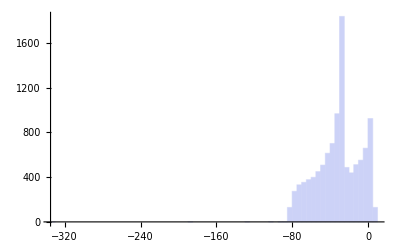

```mathematica
{histo1,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
{zmin,zmax}=Input["Stop here and enter zmin and zmax values from histogram to trim off outliers",{zmin,zmax}]
```

{-89,5.943}

```mathematica
Interrupt[]
```

```mathematica
Length[cloudXYZ]
```

10638

#### Trim the data to lie in the x-y -z region shown in the plot above

```mathematica
test=.;
```

```mathematica
zmax
```

5.943

```mathematica
test =Reap[ Do[If[
cloudXYZ[[i]][[1]]<xmax&& cloudXYZ[[i]][[1]]>xmin &&
cloudXYZ[[i]][[2]]<ymax&& cloudXYZ[[i]][[2]]>ymin &&
cloudXYZ[[i]][[3]]<zmax&& cloudXYZ[[i]][[3]]>zmin

,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
```

```mathematica
Short[test]
```

{Null,{{«1»}}}

```mathematica
cloudXYZ=Drop[test,1]//Flatten[#,2]&;Remove[test];
```

```mathematica
npts2=Length[cloudXYZ]
```

10626

```mathematica
fileout2$=filein$<>"_"<>ToString[npts2]
```

MF03 140605b top surfs_10626

```mathematica
xvals=Take[cloudXYZ,All,{1}]//Flatten;
yvals=Take[cloudXYZ,All,{2}]//Flatten;
zvals=Take[cloudXYZ,All,{3}]//Flatten;
```

```mathematica
{xmin=Min[xvals],Mean[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],Mean[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],Mean[zvals],zmax=Max[zvals]}//N
```

{0.329979,131.94,215.585}

{0.198151,52.3678,125.959}

{-84.768,-31.5143,5.917}

```mathematica
{deltax=xmax-xmin, deltay=ymax-ymin,deltaz=zmax-zmin}
```

{215.255,125.761,90.685}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Keep all coordinate values in absolute machine coords. DO NOT subtract mean.

#### Plot after trimming the X or Y range above. TRIM IT IN PLACE.

```mathematica
lpp02=ListPointPlot3D[Take[cloudXYZ,{1,-1}],PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval",""},PlotLabel->fileout2$<>"\nnpts="<>ToString[npts2]]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
vp=ViewPoint/.Options[ListPointPlot3D]
```

{1.3,-2.4,2.}

```mathematica
(*Dynamic[vp]*)
```

```mathematica
surfplt01=ListPointPlot3D[cloudXYZ,PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval","Z[µm]"},ViewPoint->vp,PlotLabel->fileout2$<>"\nnpts="<>ToString[npts2],ImageSize->400]
```

-Graphics3D-

```mathematica
fileout2$
```

MF03 140605b top surfs_10626

```mathematica
Button["Export raw data plot",Export[fileout2$<>"_rawregion.tiff",surfplt01,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export raw data plot

#### End of range clean-up iteration section. Contine after subregion is selected.

```mathematica
npts3=Length[zvals]
```

10626

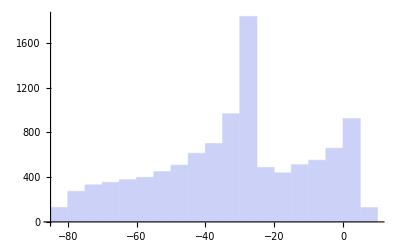

```mathematica
histplt=Histogram[zvals]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
zsd=StandardDeviation[zvals]//N
```

22.6688

```mathematica
minq=-50.
```

-50.

#### Select the appropriate Z trim criteria next. Leave lists empty to use all points without discarding any.

```mathematica
{zmin,zmax,deltaz}
```

{-84.768,5.917,90.685}

```mathematica
{minq,maxq}={-12,16}; (* Set manually here *)
```

```mathematica
zminlist={};zmaxlist={};
```

```mathematica
3zsd
```

68.0065

```mathematica
med=Median[zvals]
```

-29.4225

```mathematica
meanz=Mean[zvals]
```

-31.5143

```mathematica
iqr=InterquartileRange[zvals]
```

32.588

```mathematica
maxq=med+2 iqr
```

35.7535

```mathematica
minq=med-2 iqr
```

-94.5985

```mathematica
{minq,maxq}={med-3 iqr,med+3 iqr}
```

{-127.187,68.3415}

```mathematica
{minq,maxq}={meanz-3 zsd,meanz+3 zsd}
```

{-99.5209,36.4922}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Input["Abort to select one of the following Z trim criteria manually.\nDefault is no trim."]
Interrupt[]
```

$Aborted

```mathematica
zmaxlist=Select[zvals,#> maxq &];
zminlist=Select[zvals,#< minq &];
```

```mathematica
zsd
```

22.6586

```mathematica
zmaxlist=Select[zvals,#>3zsd &];
zminlist=Select[zvals,#<-3 zsd &];
```

```mathematica
zminlist={};zmaxlist={};
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Continue here after selecting points to discard, or if no points to discard. Skip if nothing to trim.

```mathematica
Length[zminlist]
```

0

```mathematica
Union[zmaxlist];
```

```mathematica
Length[%]
```

0

```mathematica
(* Share[] *)
```

```mathematica
outliers=Join[zminlist,zmaxlist];Length[outliers]
```

0

```mathematica
outliers2=Union[outliers];
```

```mathematica
plist=Table[Position[zvals,outliers2[[i]]],{i,Length[outliers2]}];
Short[plist]
```

{}

```mathematica
plist=Flatten[plist,1];
```

```mathematica
meanXYZd=.;meanXYZt=.;
```

```mathematica
cloudXYZ=Delete[cloudXYZ,plist];
```

Discard points from the list that lie outside the desired range. Note that the result is a list, not an array. Can't use plot functions that require an array for input.

top is a reduced-size array to use in fitting the surface to avoid excessive calculation time. reduce=1 uses all the points.

```mathematica
topall=cloudXYZ;
```

```mathematica
npts4=Length[topall]
```

10626

```mathematica
fileout$=filein$<>"_"<>ToString[npts4]
```

MF03 140605b top surfs_10626

```mathematica
top=.
```

```mathematica
sparsetop=topall;
```

```mathematica
zsdev=StandardDeviation[sparsetop][[3]]//N
```

22.6688

```mathematica
rowscols$="sparse";
```

```mathematica
topplt=ListPointPlot3D[sparsetop,PlotLabel->fileout$,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

-Graphics3D-

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/MF03 140605b top surfs_files

```mathematica
Button["Export topplt",Export[fileout$<>"_topplt.tiff",topplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export topplt

### Fit edited list to a surface. Enter the surface fit order next. A general set of basis polynomials is calculated and the fit is performed. Enter the x and y orders separately

Select one of the button options, then continue

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
fitidx={};fitflag=False;x=.;y=.;
```

```mathematica
Button["General polynomial fit",fitflag=True;Print["Set fitbasis next."]]

Button["Pure Plane fit",fitbasis={1,x,y};fitidx="1,1";fitflag=False;fitord$=StringTake[ToString[fitbasis],{2,-2}];Print["fitbasis =",fitbasis]]

Button["Pure Sphere surface",fitflag=False;fitbasis={1,x,y,x y,x^2+y^2};fitidx="2,2";fitord$=StringTake[ToString[fitbasis//InputForm],{2,-2}];Print["fitbasis =",fitbasis]]
```

General polynomial fit

Pure Plane fit

Pure Sphere surface

fitbasis ={1,x,y,x y,x^2+y^2}

#### COntinue after fit selection

```mathematica
fitflag
```

False

```mathematica
fitidx
```

2,2

```mathematica
fitord$
```

1, x, y, x*y, x^2 + y^2

```mathematica
If[fitflag
,fitidx=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
fitidx;
sp=StringSplit[fitidx,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];Print["ordx ",ordx," ordy ",ordy];
fitord$=StringTake[ToString[sp],{2,-2}];
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j](*Print[{i,j,fitbasis}]*)],{i,0,ordx},{j,ordy,0,-1}]
,
fitidx=fitidx];
fitbasis
```

{1,x,y,x y,x^2+y^2}

surffit defines the surface equation in the given XY coord system with the correct Z-units:

```mathematica
Length[sparsetop]
```

10441

```mathematica
surffit[x_,y_]=Fit[sparsetop,fitbasis,{x,y}]
```

3.85847+0.387443 x-0.322687 y+0.000960806 x y-0.00249149 (x^2+y^2)

```mathematica
surffit[x,y]
```

3.85847+0.387443 x-0.322687 y+0.000960806 x y-0.00249149 (x^2+y^2)

```mathematica
c0x=
Coefficient[surffit[x,y],x,2]/.y->0
```

-0.00249149

```mathematica
c0y=Coefficient[surffit[x,y],y,2]/.x->0
```

-0.00249149

```mathematica
surffitplot=Plot3D[surffit[x,y],{x,xmin,xmax},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.4]];
```

```mathematica
Show[surffitplot,topplt,AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"}]
```

-Graphics3D-

When rawXYZ values are in meter units, the radius is in units of meters.

```mathematica
If[c0x!=0.0,Rx=1/(2*c0x),Rx=Infinity]
```

-200.683

```mathematica
fileout$
```

MF03 140605b top surfs_10626

```mathematica
StringForm["X Radius from full 3D surface fit is `` m.",NumberForm[Rx,5]]
```

X Radius from full 3D surface fit is "-200.68" m.

Subtract the selected fit from the data. Default is plane fit subtraction.

Compute resids after subtracting fit from data points to see if the polynomial is correct.

```mathematica
residXYZ=Table[{sparsetop[[i,1]],sparsetop[[i,2]],sparsetop[[i,3]]-surffit[sparsetop[[i,1]],sparsetop[[i,2]]]}
,{i,1,Length[sparsetop]}
];
```

Now histogram the  zresids

```mathematica
zresids=Take[residXYZ,All,{3}]//Flatten;
```

```mathematica
maxz=Max[zresids];minz=Min[zresids];sigma=StandardDeviation[zresids];
zbin=BinCounts[zresids,(maxz-minz)/50];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrange=hrange[zresids,0.025,0.975];
PVrange=hgtrange[[2]]-hgtrange[[1]];
```

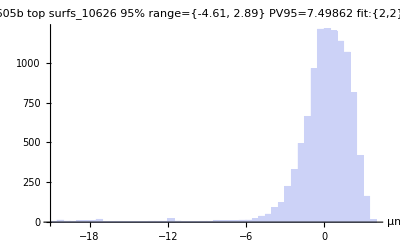

```mathematica
histresidplt=Histogram[zresids,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileout$<>"\n95% range="<>ToString[hrange[zresids,0.025,0.975]//NumberForm[#,3]&]<>" PV95="<>ToString[PVrange]<>"\nfit:{"<>fitidx<>"} sdev="<>ToString[sigma//NumberForm[#,3]&]<>zunit$]
```

```mathematica
aftertrimplot=ListPointPlot3D[residXYZ,PlotLabel->fileout$,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->400]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Interrupt[]
```

```mathematica
;
```

Compute fit value for each point and toss it out if the difference exceeds some threshold.

```mathematica
thresh=Input["Enter threshold value for trimming bad points.",thresh]
```

6

```mathematica
cloudXYZtrim=Drop[Reap[ Do[If[Abs[sparsetop[[i,3]]-surffit[sparsetop[[i,1]],sparsetop[[i,2]]]]<thresh,Sow[sparsetop[[i]]]],{i,Length[sparsetop]}]],1]//Flatten[#,2]&;
```

```mathematica
npts5=Length[cloudXYZtrim]
```

10243

```mathematica
fileout5$=filein$<>"_"<>ToString[npts5]
```

MF03 140605b top surfs_10243

```mathematica
aftertrimplot=ListPointPlot3D[cloudXYZtrim,PlotLabel->fileout5$,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

-Graphics3D-

```mathematica
(*vp2={2,0,.5}*)
```

```mathematica
vp2={1.3,-2.4,2.}
```

{1.3,-2.4,2.}

```mathematica
trimdataandLSFsurf=Show[aftertrimplot,surffitplot,PlotLabel->fileout5$<>"\nfit:{"<>fitidx<>"} after trimming pts",ViewPoint->Right]
```

-Graphics3D-

```mathematica
Button["Export trimmed data plt with LSF surf",Export[ToString[StringDrop[fileout5$,0]]<>"_"<>fitidx<>"_trimwLSFsurf.tiff",trimdataandLSFsurf,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export trimmed data plt with LSF surf

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
cleanagainflag=0;
```

```mathematica
cleanagainflag=Input["To iterate again to get a better surface fit and remove more outliers, set cleanagainflag=1",cleanagainflag]
```

0

```mathematica
sparsetop=cloudXYZtrim;(* Set the working data to the trimmed data *)
```

```mathematica
topplt=aftertrimplot;
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[cleanagainflag==1,NotebookLocate[{nb,"set fit basis"}]]
```

```mathematica
If[cleanagainflag==1,Interrupt[]]
```

```mathematica
meanXYZdetrend=.
```

```mathematica
meanXYZtd=.
```

#### The expression for the fit to the ref surf is:

```mathematica
surffit[x,y]
```

3.85847+0.387443 x-0.322687 y+0.000960806 x y-0.00249149 (x^2+y^2)

Now subtract fit from remaining points to look at residuals.

```mathematica
residsXYZ=Table[{sparsetop[[i,1]],sparsetop[[i,2]],sparsetop[[i,3]]-surffit[sparsetop[[i,1]],sparsetop[[i,2]]]}
,{i,1,Length[sparsetop]}
];
```

```mathematica
Length[residsXYZ]
```

10243

```mathematica
ViewPoint->{1.3,-2.4,2.};
```

```mathematica
aftertLSFplot=ListPointPlot3D[residsXYZ,PlotLabel->fileout5$<>"\nfit:{"<>fitidx<>"}",PlotRange->All,BoxRatios->{1,1,.5},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

-Graphics3D-

```mathematica
Button["Export trimmed data plt with LSF subt",Export[ToString[StringDrop[fileout5$,0]]<>"_"<>fitidx<>"_afterLSF.tiff",aftertLSFplot,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export trimmed data plt with LSF subt

```mathematica
zcloudresids=Take[residsXYZ,All,{3}]//Flatten;
```

```mathematica
maxz=Max[zcloudresids];minz=Min[zcloudresids];sigma=StandardDeviation[zcloudresids];
```

```mathematica
{minz,maxz,sigma}
```

{-5.992,3.78757,1.59124}

```mathematica
Short[zcloudresids]
```

{-2.73254,0.930775,«10240»,-3.47462}

```mathematica
zbin=BinCounts[zcloudresids,(maxz-minz)/25]
```

{3,12,18,19,38,43,77,91,135,209,279,390,472,601,883,947,945,972,915,865,821,722,426,241,105,14}

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

```mathematica
hgtrange95=hrange[zcloudresids,0.025,0.975]
```

{-3.30072,2.89037}

```mathematica
PVrange95=hgtrange95[[2]]-hgtrange95[[1]]
```

6.1911

```mathematica
bmeth={"Sturges","Scott","FreedmanDiaconis","Wand"};
```

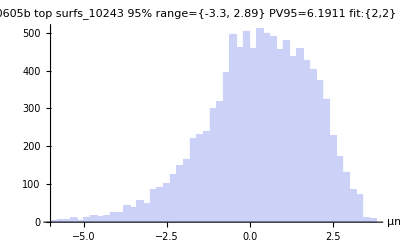

```mathematica
histresidplt=Histogram[zcloudresids,bmeth[[2]],ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileout5$<>"\n95% range="<>ToString[hrange[zcloudresids,0.025,0.975]//NumberForm[#,3]&]<>" PV95="<>ToString[PVrange95]<>"\nfit:{"<>fitidx<>"} sdev="<>ToString[sigma//NumberForm[#,3]&]<>zunit$]
```

```mathematica
Button["Export histresid plot file",Export[ToString[StringDrop[fileout5$,0]]<>"_"<>fitidx<>"_histSR.tiff",histresidplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export histresid plot file

```mathematica
accumulatedCount[bins_,counts_]:=Accumulate[counts]
```

```mathematica
hrange[zcloudresids,0.025,0.975]
```

{-3.30072,2.89037}

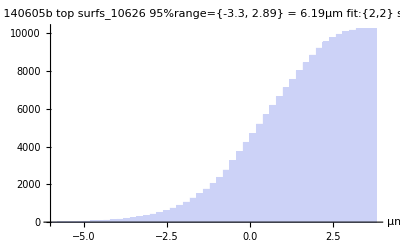

```mathematica
histcumplt=Histogram[zcloudresids,Automatic,accumulatedCount,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->14],PlotLabel->fileout$<>"\n95%range="<>ToString[hrange[zcloudresids,0.025,0.975]//NumberForm[#,3]&]<>" = "<>ToString[PVrange95//NumberForm[#,3]&]<>zunit$<>"\nfit:{"<>fitidx<>"} sdev="<>ToString[sigma//NumberForm[#,3]&],AxesLabel->{zunit$,""}]
```

```mathematica
Button["Export histcum plot file",Export[ToString[StringDrop[fileout5$,0]]<>"_"<>fitidx<>"_histcumSR.tiff",histcumplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export histcum plot file

```mathematica
quantlist={0.0,0.005,0.01,0.025,0.50,.975,0.99,0.995,1.0};
```

```mathematica
qres=Quantile[zcloudresids,quantlist]
```

{-5.992,-4.70115,-4.11079,-3.30072,0.373366,2.89037,3.15877,3.29232,3.78757}

```mathematica
qtable=Transpose[{quantlist,qres}]//TableForm
```

0. | -5.992
0.005 | -4.70115
0.01 | -4.11079
0.025 | -3.30072
0.5 | 0.373366
0.975 | 2.89037
0.99 | 3.15877
0.995 | 3.29232
1. | 3.78757

```mathematica
q99range=qres[[8]]-qres[[2]]
```

7.99347

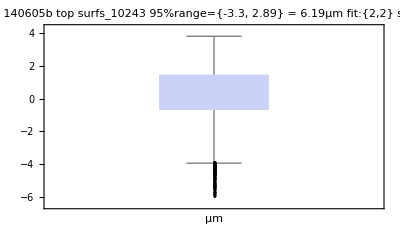

```mathematica
bwc=BoxWhiskerChart[zcloudresids,"Outliers",BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->14],PlotLabel->fileout5$<>"\n95%range="<>ToString[hrange[zcloudresids,0.025,0.975]//NumberForm[#,3]&]<>" = "<>ToString[PVrange95//NumberForm[#,3]&]<>zunit$<>"\nfit:{"<>fitidx<>"} sdev="<>ToString[sigma//NumberForm[#,3]&],AxesLabel->{zunit$,""}]
```

```mathematica
Button["Export box whisker chart file",Export[ToString[StringDrop[fileout5$,0]]<>"_"<>fitidx<>"_boxwhisker.tiff",bwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export box whisker chart file

#### Write out the quantile info to xls file and all zresids to text file.

```mathematica
$ExportFormats;
```

```mathematica
residsXYZ[[1;;10]]
```

{{0.83031,69.1675,-2.73254},{0.830394,68.6675,0.930775},{0.830472,68.1675,1.25433},{0.830546,67.6675,1.75114},{0.830587,67.1675,2.01821},{0.830587,66.6675,2.18054},{0.83057,66.1675,2.32012},{0.83056,65.6675,2.31295},{0.830554,65.1675,2.26202},{0.830533,64.6675,2.34135}}

```mathematica
Export[fileout5$<>"_"<>fitidx<>"_LSFsubt.xlsx",Prepend[residsXYZ,fileout5$<>"_"<>fitidx<>"_LSFsubt.xlsx"],"XLSX"]
```

MF03 140605b top surfs_10243_2,2_LSFsubt.xlsx

```mathematica
Export[fileout5$<>"_Quantiles.xlsx",qtable,"XLSX"]
```

MF03 140605b top surfs_10243_Quantiles.xlsx

```mathematica
binwid=(maxz-minz)/25;
```

```mathematica
bcts=BinCounts[zcloudresids,binwid]
```

{3,12,18,19,38,43,77,91,135,209,279,390,472,601,883,947,945,972,915,865,821,722,426,241,105,14}

```mathematica
Mean[zcloudresids]
```

0.261336

```mathematica
sd=StandardDeviation[zcloudresids]//N
```

1.59124

```mathematica
MeanDeviation[zcloudresids]//N
```

1.27054

```mathematica
MedianDeviation[zcloudresids]
```

1.07756

```mathematica
zwid=4 sd
```

6.36497

```mathematica
SelectionMove[nb,Before,GeneratedCell]
```